```mathematica
it = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ)∫_(d/2 - a/2)^(d/2+a/2) E^((2 π I (w-y1)^2)/(2 * D1 * λ))*E^((2 π I (y1-z)^2)/(2 * D2 * λ))ⅆy1;
ib = E^((2π* I * D1)/λ) * E^((2π* I * D2)/λ) ∫_(-d/2-a/2)^(-d/2+a/2) E^((2 π I (w-y2)^2)/(2 * D1 * λ))*E^((2 π I (y2-z)^2)/(2 * D2 * λ))ⅆy2;
```

```mathematica
(*i = (it + ib)*Conjugate[it+ib];*)
i = (it + ib);
coni = Conjugate[i];
func = i*coni;
```

```mathematica
D1 = 380;
D2 = 500;
λ = .000546;
z = x -6.2;
d = .353;
a = .1;
```

```mathematica
func;
realfunc = 9000*Re[func];
```

((0.121391+0.121391 ⅈ) ⅇ^((0.+1.01267×10^7 ⅈ)+(0.+6.53845 ⅈ) (6.2+w-x)^2) (ⅈ Erfi[(0.00414806+0.00414806 ⅈ) (-199.32+500 w+380 (-6.2+x))]-ⅈ Erfi[(0.00414806+0.00414806 ⅈ) (-111.32+500 w+380 (-6.2+x))])+(0.121391+0.121391 ⅈ) ⅇ^((0.+1.01267×10^7 ⅈ)+(0.+6.53845 ⅈ) (6.2+w-x)^2) (ⅈ Erfi[(0.00414806+0.00414806 ⅈ) (111.32+500 w+380 (-6.2+x))]-ⅈ Erfi[(0.00207403+0.00207403 ⅈ) (398.64+1000 w+760 (-6.2+x))]))^2

```mathematica
SetDirectory["/Users/dluntzma/Desktop/DoubleSlit-ED"];
counts1 = Import["2014_double_slit_bulb_counts.csv"];
counts1;
```

```mathematica
fit1 = NonlinearModelFit[counts1,realfunc,{{w,0}}, x];
```

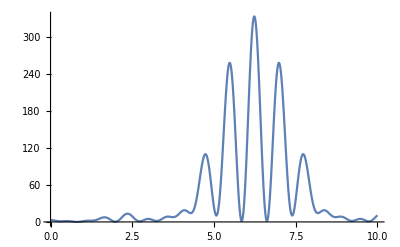

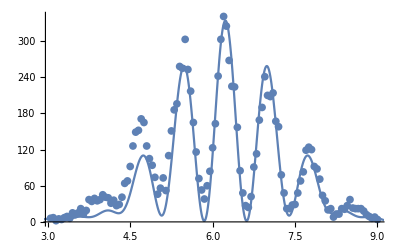

```mathematica
plot1 = Plot[fit1[x], {x, 0, 10},PlotRange->All]
Show[ListPlot[counts1], plot1]
```

```mathematica
fit1["FitResiduals"]
```

{1.5019,3.36465,-0.62697,3.16841,2.44299,5.03072,5.95766,1.43638,8.80441,4.42309,6.56508,13.3241,4.57546,11.003,29.19,25.7503,29.4647,23.3779,22.8228,28.3511,22.5802,20.9859,12.6971,19.3528,12.0742,14.5837,24.4655,41.5226,35.1551,44.6646,61.392,66.6275,54.2722,63.2944,55.0728,22.7643,16.8422,26.9355,30.0446,22.1362,44.0374,60.4718,24.0347,51.8975,51.065,38.0899,1.25175,25.3199,0.114469,46.1369,15.5481,17.7174,16.4696,22.0212,26.4631,40.5303,36.3312,43.7052,28.9338,10.6504,-16.0575,-2.20543,6.15229,12.9637,-7.43596,-41.2924,-37.5691,23.7723,24.212,13.5604,21.942,23.5062,17.5551,8.89449,13.3641,-18.3415,-15.32,-37.255,-12.0212,-47.814,-33.62,6.02188,3.88345,43.3362,7.79895,12.065,6.27195,11.3615,8.98656,-8.06798,-11.7977,-14.019,-16.3269,10.2032,14.6768,18.4282,4.39955,17.7353,18.4468,7.00472,9.74811,2.05404,7.26578,-6.56814,-3.05928,-4.85284,3.07512,2.25204,9.69203,22.0077,10.6029,11.8852,13.4413,14.1342,10.1078,3.70957,0.361744,-2.57559,0.0885692,-2.67215}

```mathematica
ChiSq=∑_(j=1)^120 ((fit1["FitResiduals"][[j]])/(2(√counts1[[j,2]]-√1.68)))^2
```

374.246

```mathematica
RedChiSq = ChiSq/7
```

53.4637

```mathematica
counts1[[2,2]]
```

7